```mathematica
(*PES fitting; Harmonic for angle / dihedral*)

(*Input data*)
SetDirectory["/Users/Sherina/Desktop/GAS/BOND/CT.KS"];
```

```mathematica
PES=Import["PES_processed.txt","Table"];(*Unit: {nm, kJ /mol}*)

b0=1.819619769677 /10
(*nm*)
```

0.181962

```mathematica
Clear[k,a,d];
fit=FindFit[PES,d*(1-Exp[-a*(x-b0)])^2, {d,a}, x]
```

{d→397.504,a→16.3085}

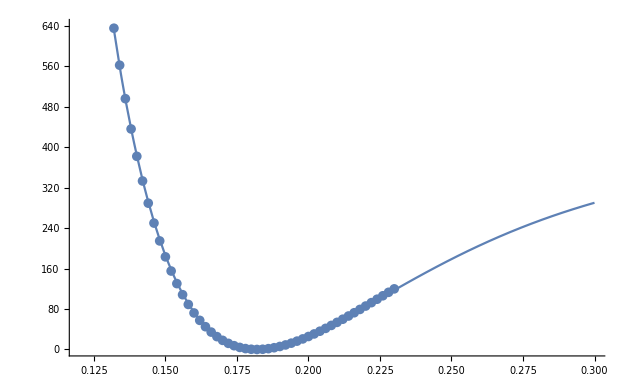

```mathematica
Show[Plot[fit[[1,2]]*(1-Exp[-fit[[2,2]]*(x-b0)])^2,{x,0.12,0.30},PlotRange->{Automatic,Automatic}],ListPlot[PES],AxesOrigin-> {0,0}]
```

```mathematica
k = a^2*2*d/.{a-> fit[[2,2]],d-> fit[[1,2]]}(*kJ*mol^-1*nm^-2*)
```

211446.